## Woods-Saxon Potential

```mathematica
A=100;
a=0.5;
V0=50;
R=1.2*A^{1/3};
RTEST=6.5;
vws[r_]:=-V0/(1+Exp[(r-R)/a]);
```

```mathematica
N[R]
```

{5.56991}

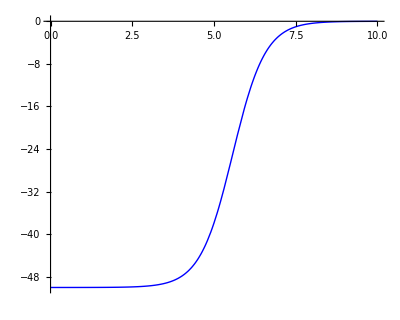

```mathematica
Plot[vws[r],{r,0,10},PlotStyle->{Blue,Thick},Axes->{True,True},AspectRatio->0.8,AxesStyle->{Directive[Arrowheads[{0,0.05}],Black,Thick,17,FontFamily->"Times",Bold],Directive[Arrowheads[{-0.05,0}],Black,Thick,17,FontFamily->"Times",Bold,AxesLabel->{"x","y"}]},PlotRange->{{0,9},{0,-65}}]
```

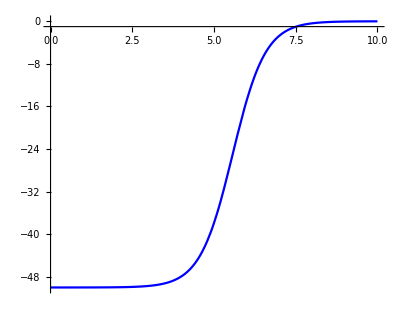
-Graphics-V_ws(r) [MeV]r [fm]

```mathematica
Labeled[Plot[vws[r],{r,0,10},PlotStyle->{Blue,Thick},Axes->{True,True},AspectRatio->0.8,AxesStyle->{Directive[Arrowheads[{0,0.05}],Black,Thick,17,FontFamily->"Times",Bold],Directive[Arrowheads[{-0.05,0}],Black,Thick,17,FontFamily->"Times",Bold,AxesLabel->{"x","y"}]},PlotRange->{{0,7.5},{0,-65}},AxesOrigin->{0,-1}],{"V_ws(r) [MeV]","r [fm]"},{Left,Top},RotateLabel->True]
```